# Comparison of equations of state for gaseous CO_2

This exploration compares common equations of state with experimental data for gaseous CO_2. The ideal gas model is a rather harsh approximation and assumes that particles don’t interact with each other and that gas particles are essentially point particles with no volume. The van der Waals equation of state corrects for non-zero volume and also includes a pressure correction that allows for inter-particle attraction. The attraction would cause the measured pressure to be lower than that predicted by the ideal gas equation of state. Redlich Kwong equation of state is an empirical equation that fits experimental measurements above the critical temperature quite well.

## Functions for Calculation

We have collected data for CO_2 at three different temperatures:  293 K , 323 K, and 373 K. The critical temperature of CO_2 is 304.25 K.

Ideal gas equation of state: The model assumes that gas particles are point particles and do not interact with each other. The function calculates the pressure according to the ideal gas model. rgas is the Universal gas constant.

```mathematica
rgas=Quantity[0.08206,("Liters""Atmospheres")/("Moles""Kelvins")];
idealgasP[t_,v_]:=(rgas t)/v
```

van der Waals equation of state: This model assigns a non-zero volume (parameter b) for particles and also includes attractive interaction (parameter a) between gas particles.

```mathematica
vdwgasP[t_,v_,a_,b_]:=(rgas t)/(v-b)-a/v^2
aCO2=Quantity[3.952,(("Liters")^2"Atmospheres")/("Moles")^2];
bCO2=Quantity[0.042,("Liters")/("Moles")];
```

Redlich Kwong equation of state. This model also assigns non-zero volume and attractive interaction between particles. It is generally seen as a huge improvement over the VdW model.

```mathematica
rkgasP[t_,v_,a_,b_]:=(rgas t)/(v-b)-a/(t^(1/2)v(v+b))
ACO2=Quantity[63.752,("Atmospheres"("Liters")^2("Kelvins")^(1/2))/("Moles")^2];
BCO2=Quantity[0.029677,("Liters")/("Moles")];
```

## 293 Kelvin

Organizing the data in list format for computations and plotting.

```mathematica
t293=Quantity[293,"Kelvins"];
p293=QuantityArray[{35.,37,40,44,45,48,50,53,55,56,56.5,56.5,57,60,75,100},"Atmospheres"];
v293=QuantityArray[{0.533,0.493,0.441,0.380,0.366,0.320,0.304,0.269,0.245,0.231,0.224,0.0583,0.0580,0.0566,0.0536,0.0511},("Liters")/("Moles")];
```

Look at the P vs V plot for the gas and compare the experimental data with ideal gas model

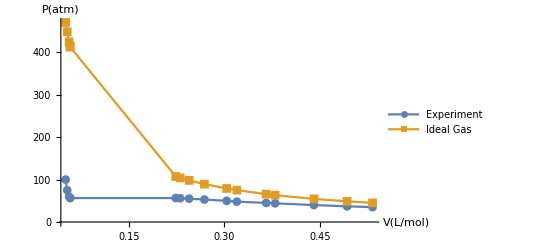

```mathematica
ListLinePlot[{Transpose[{v293,p293}],Transpose[{v293,idealgasP[t293,v293]}]},PlotLegends->{"Experiment","Ideal Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All]
```

Clearly the agreement between the ideal gas model and experimental data is not good. The model tracks the data qualitatively, however, it gets worse as molar volume is decreased.

Let’s analyze the VdW model and compare it with the experimental values.

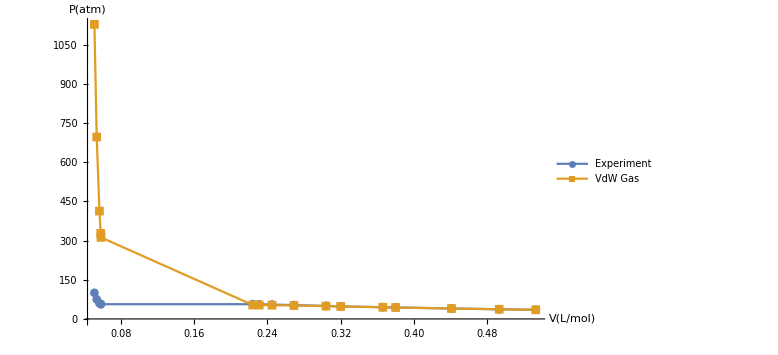

```mathematica
ListLinePlot[{Transpose[{v293,p293}],Transpose[{v293,vdwgasP[t293,v293,aCO2,bCO2]}]},PlotLegends->{"Experiment","VdW Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

A cursory look tells us that the model is in quantitative agreement at higher molar volumes and in qualitative agreement at lower molar volumes.

Let’s check the RK model

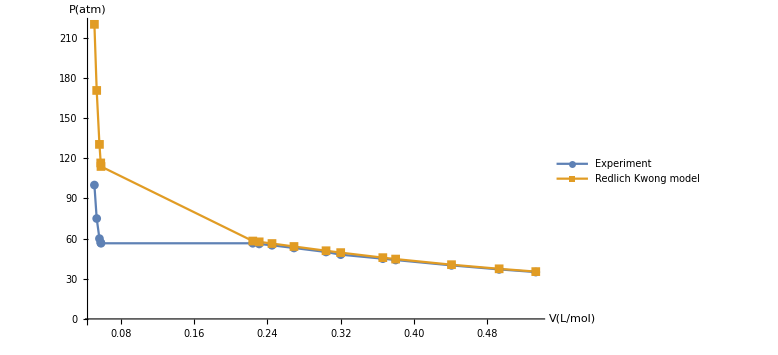

```mathematica
ListLinePlot[{Transpose[{v293,p293}],Transpose[{v293,rkgasP[t293,v293,ACO2,BCO2]}]},PlotLegends->{"Experiment","Redlich Kwong model"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

We can see that there is quantitative agreement at larger volumes and even at smaller volumes the difference between experimental and model calculated pressures is much lower than vdW model.

Let’s put all the plots together so that we can compare all models with experimental data.

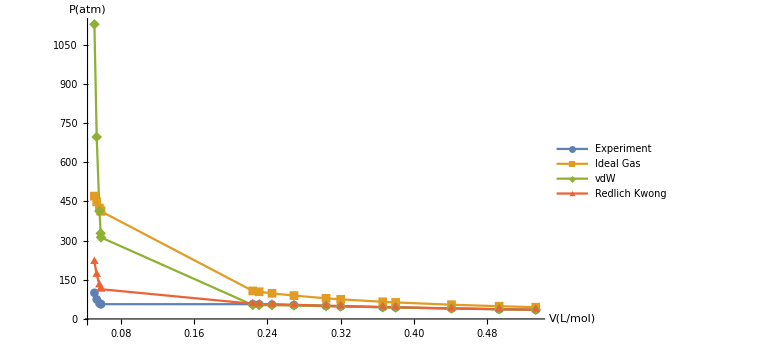

```mathematica
ListLinePlot[{Transpose[{v293,p293}],Transpose[{v293,idealgasP[t293,v293]}],Transpose[{v293,vdwgasP[t293,v293,aCO2,bCO2]}],Transpose[{v293,rkgasP[t293,v293,ACO2,BCO2]}]},PlotLegends->{"Experiment","Ideal Gas","vdW","Redlich Kwong"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

This composite plot makes it clear that the Redlich Kwong model has the best agreement with the experimental data.

## 323 K

Organize the data so that we can plot it.

```mathematica
t323=Quantity[323.,"Kelvins"];
p323=QuantityArray[{45,48,50,53,55,60,65,68,70,75,80,85,90,95,100,110,125,150,175,200,225,250,275,300},"Atmospheres"];
v323=QuantityArray[{0.473,0.434,0.412,0.380,0.361,0.319,0.282,0.262,0.250,0.221,0.196,0.171,0.149,0.128,0.110,0.0847,0.0706,0.0624,0.0584,0.0559,0.0539,0.0524,0.0514,0.0504},("Liters")/("Moles")];
```

Check the behavior of the ideal gas model.

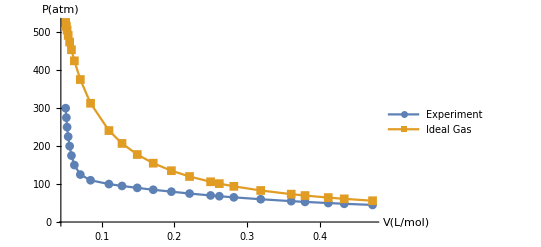

```mathematica
ListLinePlot[{Transpose[{v323,p323}],Transpose[{v323,idealgasP[t323,v323]}]},PlotLegends->{"Experiment","Ideal Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All]
```

Notice that the curves are slightly closer as the temperature has increased. There is still qualitative agreement, however, we can see a clear shift.

Check the vdW model behavior

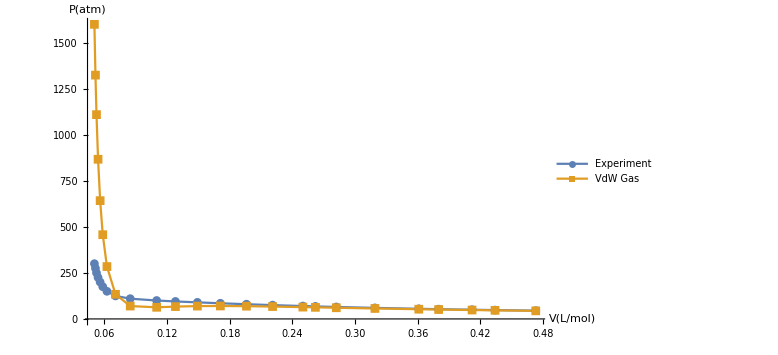

```mathematica
ListLinePlot[{Transpose[{v323,p323}],Transpose[{v323,vdwgasP[t323,v323,aCO2,bCO2]}]},PlotLegends->{"Experiment","VdW Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

The VdW model still shows close agreement with experimental data at larger molar volumes.

Check the RK model

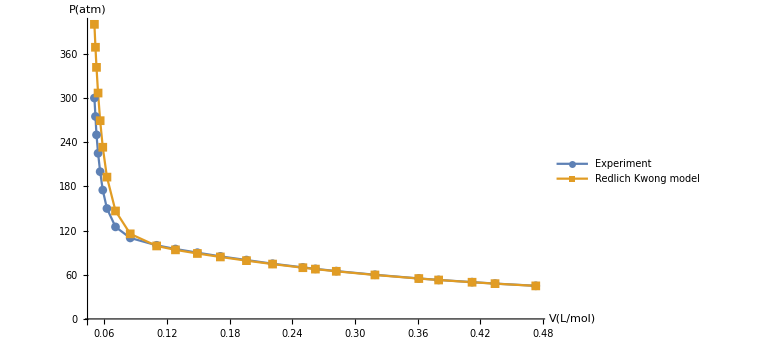

```mathematica
ListLinePlot[{Transpose[{v323,p323}],Transpose[{v323,rkgasP[t323,v323,ACO2,BCO2]}]},PlotLegends->{"Experiment","Redlich Kwong model"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

The model seems to be tracking experimental data more closely as the temperature increased.

Let’s look at all the models in one view.

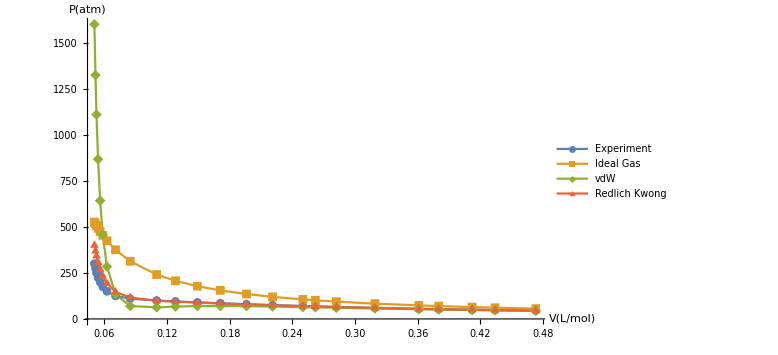

```mathematica
ListLinePlot[{Transpose[{v323,p323}],Transpose[{v323,idealgasP[t323,v323]}],Transpose[{v323,vdwgasP[t323,v323,aCO2,bCO2]}],Transpose[{v323,rkgasP[t323,v323,ACO2,BCO2]}]},PlotLegends->{"Experiment","Ideal Gas","vdW","Redlich Kwong"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

Here we can see that the VdW model is completely out of sync with experimental data and the RK model.

## 373 K

Organize the data for 373 K (100 C)

```mathematica
t373=Quantity[373,"Kelvins"];
p373=QuantityArray[{50,53,55,60,65,68,70,75,80,85,90,95,100,110,125,150,175,200,225,250,275,300,350,400,450,500,550,600},"Atmospheres"];
v373=QuantityArray[{0.539,0.504,0.479,0.436,0.396,0.375,0.362,0.333,0.307,0.285,0.264,0.246,0.230,0.202,0.169,0.131,0.106,0.091,0.0812,0.0747,0.0699,0.0663,0.0614,0.0580,0.0556,0.0536,0.0521,0.0508},("Liters")/("Moles")];
```

Compare the ideal gas model behavior with experimental data

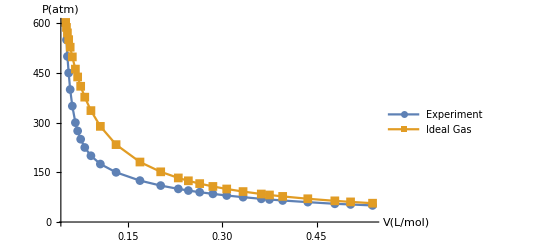

```mathematica
ListLinePlot[{Transpose[{v373,p373}],Transpose[{v373,idealgasP[t373,v373]}]},PlotLegends->{"Experiment","Ideal Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All]
```

Note the interesting change at this temperature. The ideal gas model starts to track experimental data with reasonable agreement.

Analyze the VdW model

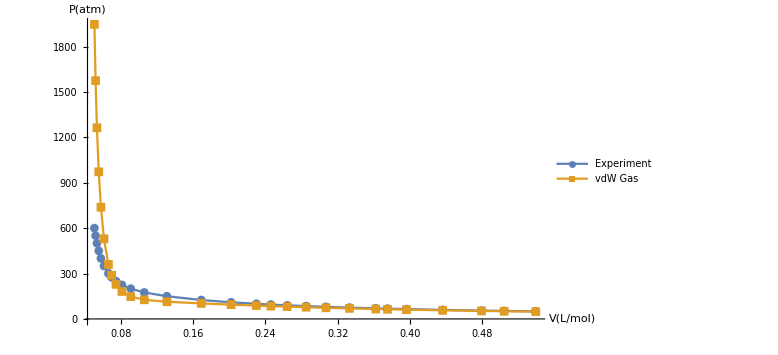

```mathematica
ListLinePlot[{Transpose[{v373,p373}],Transpose[{v373,vdwgasP[t373,v373,aCO2,bCO2]}]},PlotLegends->{"Experiment","vdW Gas"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

The VdW model is still in very good agreement at larger molar volumes.

Analyze the RK model

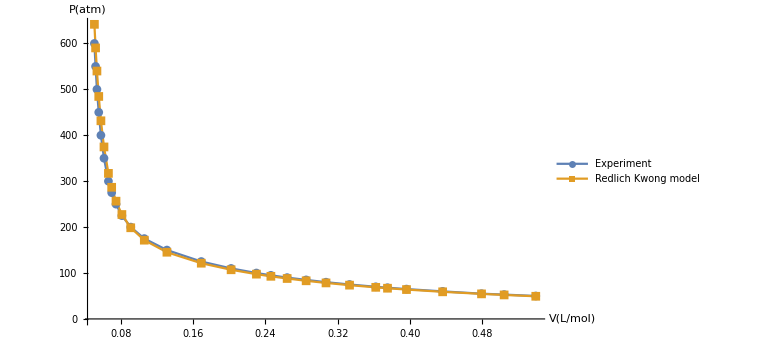

```mathematica
ListLinePlot[{Transpose[{v373,p373}],Transpose[{v373,rkgasP[t373,v373,ACO2,BCO2]}]},PlotLegends->{"Experiment","Redlich Kwong model"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,PlotRange->All,ImageSize->Large]
```

At higher temperatures the RK model has quantitative agreement with experimental values.

Adding all the models and data on a single plot.

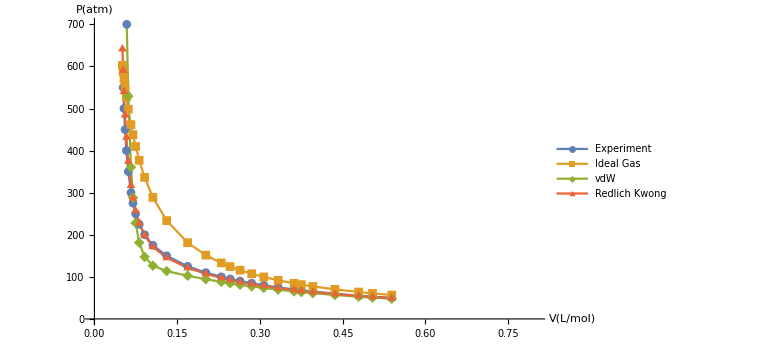

```mathematica
ListLinePlot[{Transpose[{v373,p373}],Transpose[{v373,idealgasP[t373,v373]}],Transpose[{v373,vdwgasP[t373,v373,aCO2,bCO2]}],Transpose[{v373,rkgasP[t373,v373,ACO2,BCO2]}]},PlotLegends->{"Experiment","Ideal Gas","vdW","Redlich Kwong"},AxesLabel->{"V(L/mol)","P(atm)"},PlotMarkers->Automatic,ImageSize->Large,PlotRange->{{0,0.8},{0,700}}]
```

At the highest temperature (373K) the models seem to perform better. At high temperatures, the molecules are on average moving faster and the models in general perform better

## Hands-on Exploration

Let us explore the Van der Waals model equation. The equation of state is P=(R T)/(V^--b)-a/((V^-)^2). The parameter b is the correction for non-zero volume of a gas particle,and, a, is the correction that accounts for attractive interaction between particles.

```mathematica
Manipulate[ListPlot[{Transpose[{v373,p373}],Transpose[{v373,vdwgasP[t373,v373,Quantity[a,("Atmospheres" ("Liters")^2)/("Moles")^2],Quantity[b,("Liters")/("Moles")]]}]},PlotLegends->{"Experimental","vdW"},AxesLabel->{"V(L/mol)","P(atm)"}],Style["Attraction",10],{a,2.0,6.0},Style["Size parameter"],{b,0.01,0.05}]
```

Notice that if you increase the attraction parameter, the calculated pressure decreases.

Modify the size parameter to notice that it shows the opposite behavior to a.

Further Explorations

Higher order equations of state

PVT Diagrams of gases under extreme conditions

Authorship information

Arun Sharma

06/23/2017

aksharma@wagner.edu

Future improvements

Add quiz functionality to check for comprehension